# Video Traking UI

## User Interface for gereic video tracking problems

## Step 0 - Load the program

```mathematica
Quit[];
```

```mathematica
<<VideoTracking`
<<VideoAnalysis`
$HistoryLength = 2; (*prevent memory overload*)
Options[FFmpeg]={
"Colors"->1 (*number of color channels*),"ColorCommand"->"gray" (*indicator for "-pix_fmt" parameter:gray/rgb24*)
};
```

VideoFindThreshold::shdw: Symbol "VideoFindThreshold" appears in multiple contexts {"VideoAnalysis`", "Global`"}; definitions in context "VideoAnalysis`" may shadow or be shadowed by other definitions.

## Step 1 - Select the video file

```mathematica
SelectVideo[ "E:\\Experiments\\Antony\\2015-02-12\\low_conc_square_wave_(starts_+1V_on_right)2_s2.avi"]
```

low_conc_square_wave_(starts_+1V_on_right)2_s2.avi has 12000 frames and is 400x400

## Step 2 - Select region of intrest

```mathematica
SelectROI[{{141,273},{225,273},{225,251},{141,251}}] (*from 34*)
```

{{141,273},{225,273},{225,251},{141,251}}

```mathematica
SelectROI[{{144,271},{228,271},{228,249},{144,249}}] (* up to 34 *)
```

{{144,271},{228,271},{228,249},{144,249}}

## Step 3 - Compute the background image

```mathematica
LoadAllFrames[]
```

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

```mathematica
bg = UpdateBackgroung[1, NumberOfFrames[]]
```

-Graphics-

```mathematica
meanBG = MeanBackground[Range@NumberOfFrames[]]
```

-Graphics-

```mathematica
ImageDifference[bg, meanBG]//ImageAdjust
```

-Graphics-

## Develop: BinirizeVideoLevel[]

```mathematica
binLevels = FindThreshold[#, Method-> "Cluster"]&/@SubstractBG/@GetFrame/@Range@NumberOfFrames[];
```

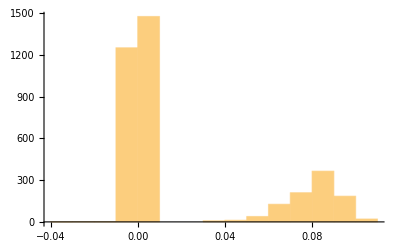

```mathematica
Histogram@binLevels
```

```mathematica
(*centers HistogramList output *)
MeanBinPlace[data_]:= { (data⟦1, 2;;⟧ + data⟦1, ;;-2⟧)/2 , data⟦2⟧ }
```

```mathematica
HistogramList[binLevels]//N
```

{{-0.04,-0.03,-0.02,-0.01,0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11},{1.,2.,2.,1252.,1477.,0.,0.,8.,12.,39.,127.,210.,365.,185.,21.}}

```mathematica
MeanBinPlace@HistogramList@binLevels
```

(-7/200 | -1/40 | -3/200 | -1/200 | 1/200 | 3/200 | 1/40 | 7/200 | 9/200 | 11/200 | 13/200 | 3/40 | 17/200 | 19/200 | 21/200
1 | 2 | 2 | 1252 | 1477 | 0 | 0 | 8 | 12 | 39 | 127 | 210 | 365 | 185 | 21)

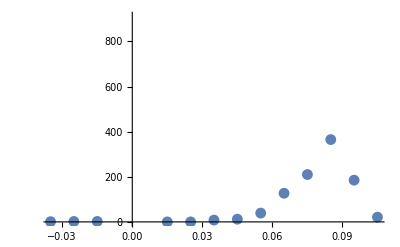

```mathematica
ListPlot@Transpose@MeanBinPlace@HistogramList@binLevels
```

```mathematica
FindPeaks@N@Transpose@MeanBinPlace@HistogramList@binLevels
```

FindPeaks::arg: -- Message text not found -- ({{-0.035, 1.}, {-0.025, 2.}, {-0.015, 2.}, {-0.005, 1252.}, {0.005, 1477.}, {0.015, 0.}, {0.025, 0.}, {0.035, 8.}, {0.045, 12.}, {0.055, 39.}, {0.065, 127.}, {0.075, 210.}, {0.085, 365.}, {0.095, 185.}, {0.105, 21.}})

FindPeaks[{{-0.035,1.},{-0.025,2.},{-0.015,2.},{-0.005,1252.},{0.005,1477.},{0.015,0.},{0.025,0.},{0.035,8.},{0.045,12.},{0.055,39.},{0.065,127.},{0.075,210.},{0.085,365.},{0.095,185.},{0.105,21.}}]

```mathematica
tmp = N@Transpose@MeanBinPlace@HistogramList@binLevels
```

(-0.035 | 1.
-0.025 | 2.
-0.015 | 2.
-0.005 | 1252.
0.005 | 1477.
0.015 | 0.
0.025 | 0.
0.035 | 8.
0.045 | 12.
0.055 | 39.
0.065 | 127.
0.075 | 210.
0.085 | 365.
0.095 | 185.
0.105 | 21.)

```mathematica
FindPeaks@tmp⟦;;,2⟧
```

(5 | 1477.
13 | 365.)

```mathematica
Interpolation[ Transpose@{ Range@Length@tmp, tmp⟦;;,1⟧}][13]
```

0.085

#### Combine

```mathematica
ImportInformation[raw_]:=Panel[Column[{Text[Style["KLab: Imported Track Assembly",FontSize->14,FontFamily->"Helvetica"]],"experiment"->("experiment"/.raw[[1,2]]),"comment"->("comment"/.raw[[1,2]]),"time"->DateObject[("time"/.raw[[1,2]])/1000+2208988800],"units"->("units"/.raw[[1,2]]),"array_format"->("version"/.raw[[1,2]]),"number"->("number"/.raw[[1,2]]),"version"->("version"/.raw[[1,2]])}]];
```

```mathematica
Panel[Column[{
Text[Style["BinirizeVideoLevel analysis results",FontSize->14,FontFamily->"Helvetica"]],
Show[
Histogram[binLevels,Automatic,"Probability" , AxesLabel-> {"Threshold", "P"}],
Graphics[{Red,PointSize@Large ,Point[{0.085, 0.1}]}],
ImageSize -> Medium
],
"Recomended Threshold value is " <> ToString@0.1
}]]
```

#### Test

```mathematica
<<VideoAnalysis`
```

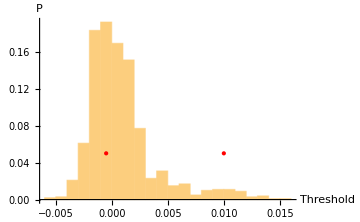
BinirizeVideoLevel[] - analysis results
-Graphics-
Recomended Threshold value is 0.01

0.01

```mathematica
BinirizeVideoLevel[]
```

## Tests: VideoFindThreshold

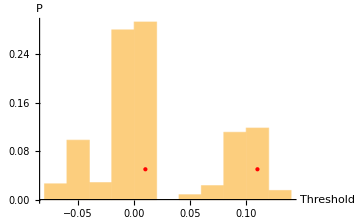
BinirizeVideoLevel[] - analysis results
-Graphics-
Recomended Threshold value is 0.11

0.11

```mathematica
VideoFindThreshold[]
```

## Tests: VideoFindActiveFrames

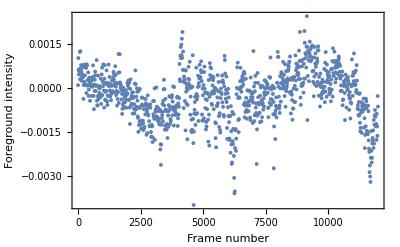

```mathematica
VideoFindActiveFrames[]
```

## Tests: VideoFrameID

```mathematica
<<VideoAnalysis`
```

```mathematica
GetRawFrames[1]
```

{-Graphics-}

```mathematica
VideoFrameID@GetRawFrames[10][[1]]
```

1361183

Test if incrementation is right

```mathematica
vals = VideoFrameID@GetRawFrames[#][[1]] &/@ Range@1000;
```

```mathematica
vals[[2;;]] - vals[[;;-2]]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

## Step 4 - configure tracing algorithm

```mathematica
Options[VideoTracking];

SetOptions[VideoTracking, 
 FilterCircularity -> {0.5, 1.6},
 FilterArea -> {8,25},
 UpdateBackgroung -> False,
 Threshold -> 0.09
]
```

{Threshold→0.09,FilterArea→{8,25},FilterCircularity→{0.5,1.6},AnalysisBlockSize→4000,UpdateBackgroung→False,BackgroundAlgorithm→SmartMeanBackground,MinThreshold→0.05}

```mathematica
(*avi filter: DV video*)
SetOptions[VideoTracking, 
 FilterCircularity -> {0.5, 1.5},
 FilterArea -> {6, 40},
 UpdateBackgroung -> False,
 Threshold -> 0.06
]
```

{Threshold→0.06,FilterArea→{6,40},FilterCircularity→{0.5,1.5},AnalysisBlockSize→4000,UpdateBackgroung→False,BackgroundAlgorithm→SmartMeanBackground,MinThreshold→0.05}

```mathematica
(*normal*)
SubstractBG[img_Image]:=ImageSubtract[ img, VideoTracking`Private`background]
```

```mathematica
(*for black particles*)
SubstractBG[img_Image]:=ImageDifference[img,VideoTracking`Private`background]
```

```mathematica
(*for black particles (experimental)*)
SubstractBG[img_Image]:=ImageSubtract[ 
ImageDifference[img,VideoTracking`Private`background],
ImageSubtract[ img, VideoTracking`Private`background]
]
```

## Step 5 - Inspect per frame basis (run many times!)

{}

-Graphics-

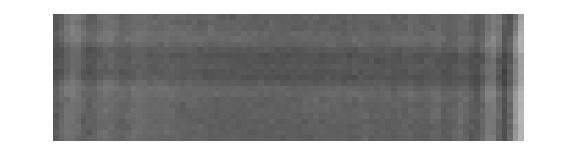

-Graphics-

-Graphics-

Area→{}

Circularity→{}

```mathematica
frame =10500;

ShowTrackOverlayed[img_,list_]:=Show[img,Graphics@Flatten@{Red,Point[#]&/@list},ImageSize->Large]

curPos = AnalyseFrame[frame]
ShowTrackOverlayed[ GetFrame[frame] , curPos]
ShowTrackOverlayed[ CurrentBackground[], curPos]
ShowTrackOverlayed[ SubstractBG@GetFrame[frame] , curPos] //ImageAdjust
ShowTrackOverlayed[ FrameBinarize@SubstractBG@GetFrame[frame] , curPos]

"Area"-> ComponentMeasurements[ FrameBinarize@SubstractBG@GetFrame[frame] ,"Area"]

"Circularity"-> ComponentMeasurements[ FrameBinarize@SubstractBG@GetFrame[frame] ,"Circularity"]
```

## Step 6 - Analyse single video

```mathematica
folder = DirectoryName[VideoFile[]];

outputFolder = FileNameJoin[{folder,"raw_points"}];
If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

out = RunAnalysis[1, NumberOfFrames[]] // AbsoluteTiming;

Print["Computation took "<> ToString@out[[1]] <> " sec"];

Print @ Export[ 
FileNameJoin[{outputFolder, (FileBaseName[ VideoFile[] ] <>".csv")}],  
out[[2]] 
];
```

Computation took 34.475271 sec

/Users/kmisiunas/Dropbox/PhD/Projects/Electrophoresis transport, 2014/experiments/antony/2015-01-30/raw_points/flooded_with_colloids_s2.csv

```mathematica
Export["C:\\Users\\km558\\Dropbox\\PhD\\Software\\video-tracking\\tests\\comparing_with_Simons_routine_2014-11-06.csv", out[[2]]  ];
```

## Analyse many videos

```mathematica
ComputeVideo[file_] := Module[{},
Print@"==============================================";
oldROI = ROICurrent[] ;

folder = DirectoryName[file];
Print @ SelectVideo[  file ];

Print["video is "<> ToString@(NumberOfFrames[] /30 // N) <> " sec long"];

Print @ SelectROI[ oldROI ];

LoadAllFrames[];

Print @ UpdateBackgroung[1, NumberOfFrames[] ] ;
(*Print @ ImageAdjust@ImageDifference[UpdateBackgroung[bg ],GetFrame[1]];*)

outputFolder = FileNameJoin[{folder,"raw_points"}];
If[ !FileExistsQ[outputFolder] , CreateDirectory[outputFolder ]];

out = RunAnalysis[1, NumberOfFrames[]] // AbsoluteTiming;

Print["Computation took "<> ToString@out[[1]] <> " sec"];

Print @ Export[ 
FileNameJoin[{outputFolder, (FileBaseName[file] <>".csv")}],  
out[[2]] 
];

]
```

```mathematica
analyseTheseFiles = FileNames["low_conc_square_wave_(starts_+1V_on_right)2_*.avi","E:\\Experiments\\Antony\\2015-02-12\\",1][[14;;]]
```

{E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s22.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s23.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s24.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s25.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s26.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s27.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s28.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s29.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s2.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s30.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s31.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s32.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s33.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s34.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s35.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s36.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s37.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s38.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s39.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s3.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s40.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s41.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s42.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s43.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s44.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s45.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s46.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s47.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s48.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s49.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s4.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s50.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s51.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s52.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s53.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s54.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s55.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s56.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s57.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s58.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s59.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s5.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s60.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s61.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s62.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s63.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s64.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s65.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s66.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s67.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s68.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s69.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s6.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s70.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s71.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s72.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s73.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s74.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s75.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s76.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s77.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s78.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s79.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s7.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s80.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s81.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s82.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s83.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s84.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s85.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s86.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s87.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s88.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s89.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s8.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s90.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s91.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s92.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s93.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s9.avi}

```mathematica
analyseTheseFiles=("E:\\Experiments\\Antony\\2015-02-12\\low_conc_square_wave_(starts_+1V_on_right)2_s"~~ToString@#~~".avi")&/@ Range[32, 45]
```

{E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s32.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s33.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s34.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s35.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s36.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s37.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s38.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s39.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s40.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s41.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s42.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s43.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s44.avi,E:\Experiments\Antony\2015-02-12\low_conc_square_wave_(starts_+1V_on_right)2_s45.avi}

```mathematica
Do[ ComputeVideo[f], {f, analyseTheseFiles }]
```

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s32.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 159.700968 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s32.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s33.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 158.795878 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s33.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s34.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 158.390838 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s34.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s35.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 90.453044 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s35.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s36.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 83.245324 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s36.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s37.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 75.571556 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s37.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s38.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 103.880387 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s38.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s39.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 103.773376 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s39.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s40.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 78.348834 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s40.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s41.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 146.920691 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s41.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s42.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 152.551254 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s42.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s43.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 86.561655 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s43.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s44.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 107.497749 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s44.csv

==============================================

low_conc_square_wave_(starts_+1V_on_right)2_s45.avi has 12000 frames and is 400x400

video is 400. sec long

{{141,273},{225,273},{225,251},{141,251}}

Buffer: expected 12000 frames. ffmpeg found 11999

Buffer: loaded entire video

-Graphics-

Computation took 220.205018 sec

E:\Experiments\Antony\2015-02-12\raw_points\low_conc_square_wave_(starts_+1V_on_right)2_s45.csv